```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,28000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[0.9,0.0001,0.267,0,7]
```

2.00001

```mathematica
Table[{ω,tr[ω,0.0001,0.05,0,15]},{ω,Range[-2,2,0.01]}]
```

{{-2.,4.41356×10^-11},{-1.99,4.50335×10^-11},{-1.98,4.59543×10^-11},{-1.97,4.68988×10^-11},{-1.96,4.78677×10^-11},{-1.95,4.88618×10^-11},{-1.94,4.98818×10^-11},{-1.93,5.09287×10^-11},{-1.92,5.20031×10^-11},{-1.91,5.31061×10^-11},{-1.9,5.42385×10^-11},{-1.89,5.54013×10^-11},{-1.88,5.65955×10^-11},{-1.87,5.7822×10^-11},{-1.86,5.9082×10^-11},{-1.85,6.03765×10^-11},{-1.84,6.17067×10^-11},{-1.83,6.30737×10^-11},{-1.82,6.44789×10^-11},{-1.81,6.59235×10^-11},{-1.8,6.74088×10^-11},{-1.79,6.89362×10^-11},{-1.78,7.05072×10^-11},{-1.77,7.21232×10^-11},{-1.76,7.37859×10^-11},{-1.75,7.54968×10^-11},{-1.74,7.72576×10^-11},{-1.73,7.90701×10^-11},{-1.72,8.09362×10^-11},{-1.71,8.28577×10^-11},{-1.7,8.48366×10^-11},{-1.69,8.68751×10^-11},{-1.68,8.89752×10^-11},{-1.67,9.11392×10^-11},{-1.66,9.33696×10^-11},{-1.65,9.56686×10^-11},{-1.64,9.8039×10^-11},{-1.63,1.00483×10^-10},{-1.62,1.03004×10^-10},{-1.61,1.05605×10^-10},{-1.6,1.08289×10^-10},{-1.59,1.11058×10^-10},{-1.58,1.13917×10^-10},{-1.57,1.16868×10^-10},{-1.56,1.19916×10^-10},{-1.55,1.23063×10^-10},{-1.54,1.26315×10^-10},{-1.53,1.29676×10^-10},{-1.52,1.33149×10^-10},{-1.51,1.36739×10^-10},{-1.5,1.40451×10^-10},{-1.49,1.4429×10^-10},{-1.48,1.48261×10^-10},{-1.47,1.52371×10^-10},{-1.46,1.56624×10^-10},{-1.45,1.61026×10^-10},{-1.44,1.65585×10^-10},{-1.43,1.70306×10^-10},{-1.42,1.75197×10^-10},{-1.41,1.80265×10^-10},{-1.4,1.85519×10^-10},{-1.39,1.90965×10^-10},{-1.38,1.96613×10^-10},{-1.37,2.02472×10^-10},{-1.36,2.08551×10^-10},{-1.35,2.14861×10^-10},{-1.34,2.21411×10^-10},{-1.33,2.28214×10^-10},{-1.32,2.3528×10^-10},{-1.31,2.42623×10^-10},{-1.3,2.50254×10^-10},{-1.29,2.58189×10^-10},{-1.28,2.66442×10^-10},{-1.27,2.75028×10^-10},{-1.26,2.83963×10^-10},{-1.25,2.93265×10^-10},{-1.24,3.02951×10^-10},{-1.23,3.13042×10^-10},{-1.22,3.23558×10^-10},{-1.21,3.3452×10^-10},{-1.2,3.45952×10^-10},{-1.19,3.57877×10^-10},{-1.18,3.70322×10^-10},{-1.17,3.83314×10^-10},{-1.16,3.96882×10^-10},{-1.15,4.11058×10^-10},{-1.14,4.25874×10^-10},{-1.13,4.41366×10^-10},{-1.12,4.5757×10^-10},{-1.11,4.74528×10^-10},{-1.1,4.9228×10^-10},{-1.09,5.10874×10^-10},{-1.08,5.30356×10^-10},{-1.07,5.50778×10^-10},{-1.06,5.72197×10^-10},{-1.05,5.9467×10^-10},{-1.04,6.18262×10^-10},{-1.03,6.43039×10^-10},{-1.02,6.69074×10^-10},{-1.01,6.96445×10^-10},{-1.,7.25235×10^-10},{-0.99,7.55534×10^-10},{-0.98,7.87438×10^-10},{-0.97,8.21051×10^-10},{-0.96,8.56484×10^-10},{-0.95,8.93857×10^-10},{-0.94,9.33299×10^-10},{-0.93,9.74951×10^-10},{-0.92,1.01896×10^-9},{-0.91,1.0655×10^-9},{-0.9,1.11473×10^-9},{-0.89,1.16685×10^-9},{-0.88,1.22208×10^-9},{-0.87,1.28062×10^-9},{-0.86,1.34273×10^-9},{-0.85,1.40867×10^-9},{-0.84,1.47873×10^-9},{-0.83,1.55322×10^-9},{-0.82,1.63249×10^-9},{-0.81,1.71691×10^-9},{-0.8,1.80689×10^-9},{-0.79,1.90289×10^-9},{-0.78,2.00538×10^-9},{-0.77,2.11491×10^-9},{-0.76,2.23207×10^-9},{-0.75,2.35751×10^-9},{-0.74,2.49195×10^-9},{-0.73,2.63617×10^-9},{-0.72,2.79107×10^-9},{-0.71,2.95759×10^-9},{-0.7,3.13682×10^-9},{-0.69,3.32995×10^-9},{-0.68,3.53829×10^-9},{-0.67,3.76333×10^-9},{-0.66,4.0067×10^-9},{-0.65,4.27025×10^-9},{-0.64,4.55604×10^-9},{-0.63,4.86637×10^-9},{-0.62,5.20385×10^-9},{-0.61,5.57141×10^-9},{-0.6,5.97236×10^-9},{-0.59,6.41044×10^-9},{-0.58,6.8899×10^-9},{-0.57,7.4156×10^-9},{-0.56,7.99303×10^-9},{-0.55,8.62853×10^-9},{-0.54,9.32933×10^-9},{-0.53,1.01038×10^-8},{-0.52,1.09614×10^-8},{-0.51,1.19135×10^-8},{-0.5,1.29729×10^-8},{-0.49,1.41548×10^-8},{-0.48,1.54767×10^-8},{-0.47,1.69596×10^-8},{-0.46,1.86279×10^-8},{-0.45,2.05107×10^-8},{-0.44,2.26426×10^-8},{-0.43,2.50653×10^-8},{-0.42,2.78287×10^-8},{-0.41,3.09934×10^-8},{-0.4,3.46332×10^-8},{-0.39,3.88388×10^-8},{-0.38,4.37222×10^-8},{-0.37,4.94229×10^-8},{-0.36,5.6116×10^-8},{-0.35,6.40239×10^-8},{-0.34,7.34309×10^-8},{-0.33,8.47055×10^-8},{-0.32,9.83303×10^-8},{-0.31,1.14946×10^-7},{-0.3,1.35418×10^-7},{-0.29,1.60931×10^-7},{-0.28,1.93142×10^-7},{-0.27,2.34418×10^-7},{-0.26,2.88224×10^-7},{-0.25,3.59791×10^-7},{-0.24,4.57288×10^-7},{-0.23,5.94019×10^-7},{-0.22,7.928×10^-7},{-0.21,1.09537×10^-6},{-0.2,1.58483×10^-6},{-0.19,2.44672×10^-6},{-0.18,4.1708×10^-6},{-0.17,8.4502×10^-6},{-0.16,0.0000253115},{-0.15,0.000703688},{-0.14,1.99956},{-0.13,2.99973},{-0.12,3.99505},{-0.11,4.00009},{-0.1,4.99991},{-0.09,5.0008},{-0.08,5.99997},{-0.07,6.01011},{-0.06,6.99994},{-0.05,6.99925},{-0.04,5.0004},{-0.03,3.01083},{-0.02,2.00499},{-0.01,1.00103},{0.,0.000431898},{0.01,1.00103},{0.02,2.00499},{0.03,3.01083},{0.04,5.0004},{0.05,6.99925},{0.06,6.99994},{0.07,6.01011},{0.08,5.99997},{0.09,5.0008},{0.1,4.99991},{0.11,4.00009},{0.12,3.99505},{0.13,2.99973},{0.14,1.99956},{0.15,0.000703688},{0.16,0.0000253115},{0.17,8.4502×10^-6},{0.18,4.1708×10^-6},{0.19,2.44672×10^-6},{0.2,1.58483×10^-6},{0.21,1.09537×10^-6},{0.22,7.928×10^-7},{0.23,5.94019×10^-7},{0.24,4.57288×10^-7},{0.25,3.59791×10^-7},{0.26,2.88224×10^-7},{0.27,2.34418×10^-7},{0.28,1.93142×10^-7},{0.29,1.60931×10^-7},{0.3,1.35418×10^-7},{0.31,1.14946×10^-7},{0.32,9.83303×10^-8},{0.33,8.47055×10^-8},{0.34,7.34309×10^-8},{0.35,6.40239×10^-8},{0.36,5.6116×10^-8},{0.37,4.94229×10^-8},{0.38,4.37222×10^-8},{0.39,3.88388×10^-8},{0.4,3.46332×10^-8},{0.41,3.09934×10^-8},{0.42,2.78287×10^-8},{0.43,2.50653×10^-8},{0.44,2.26426×10^-8},{0.45,2.05107×10^-8},{0.46,1.86279×10^-8},{0.47,1.69596×10^-8},{0.48,1.54767×10^-8},{0.49,1.41548×10^-8},{0.5,1.29729×10^-8},{0.51,1.19135×10^-8},{0.52,1.09614×10^-8},{0.53,1.01038×10^-8},{0.54,9.32933×10^-9},{0.55,8.62853×10^-9},{0.56,7.99303×10^-9},{0.57,7.4156×10^-9},{0.58,6.8899×10^-9},{0.59,6.41044×10^-9},{0.6,5.97236×10^-9},{0.61,5.57141×10^-9},{0.62,5.20385×10^-9},{0.63,4.86637×10^-9},{0.64,4.55604×10^-9},{0.65,4.27025×10^-9},{0.66,4.0067×10^-9},{0.67,3.76333×10^-9},{0.68,3.53829×10^-9},{0.69,3.32995×10^-9},{0.7,3.13682×10^-9},{0.71,2.95759×10^-9},{0.72,2.79107×10^-9},{0.73,2.63617×10^-9},{0.74,2.49195×10^-9},{0.75,2.35751×10^-9},{0.76,2.23207×10^-9},{0.77,2.11491×10^-9},{0.78,2.00538×10^-9},{0.79,1.90289×10^-9},{0.8,1.80689×10^-9},{0.81,1.71691×10^-9},{0.82,1.63249×10^-9},{0.83,1.55322×10^-9},{0.84,1.47873×10^-9},{0.85,1.40867×10^-9},{0.86,1.34273×10^-9},{0.87,1.28062×10^-9},{0.88,1.22208×10^-9},{0.89,1.16685×10^-9},{0.9,1.11473×10^-9},{0.91,1.0655×10^-9},{0.92,1.01896×10^-9},{0.93,9.74951×10^-10},{0.94,9.33299×10^-10},{0.95,8.93857×10^-10},{0.96,8.56484×10^-10},{0.97,8.21051×10^-10},{0.98,7.87438×10^-10},{0.99,7.55534×10^-10},{1.,7.25235×10^-10},{1.01,6.96445×10^-10},{1.02,6.69074×10^-10},{1.03,6.43039×10^-10},{1.04,6.18262×10^-10},{1.05,5.9467×10^-10},{1.06,5.72197×10^-10},{1.07,5.50778×10^-10},{1.08,5.30356×10^-10},{1.09,5.10874×10^-10},{1.1,4.9228×10^-10},{1.11,4.74528×10^-10},{1.12,4.5757×10^-10},{1.13,4.41366×10^-10},{1.14,4.25874×10^-10},{1.15,4.11058×10^-10},{1.16,3.96882×10^-10},{1.17,3.83314×10^-10},{1.18,3.70322×10^-10},{1.19,3.57877×10^-10},{1.2,3.45952×10^-10},{1.21,3.3452×10^-10},{1.22,3.23558×10^-10},{1.23,3.13042×10^-10},{1.24,3.02951×10^-10},{1.25,2.93265×10^-10},{1.26,2.83963×10^-10},{1.27,2.75028×10^-10},{1.28,2.66442×10^-10},{1.29,2.58189×10^-10},{1.3,2.50254×10^-10},{1.31,2.42623×10^-10},{1.32,2.3528×10^-10},{1.33,2.28214×10^-10},{1.34,2.21411×10^-10},{1.35,2.14861×10^-10},{1.36,2.08551×10^-10},{1.37,2.02472×10^-10},{1.38,1.96613×10^-10},{1.39,1.90965×10^-10},{1.4,1.85519×10^-10},{1.41,1.80265×10^-10},{1.42,1.75197×10^-10},{1.43,1.70306×10^-10},{1.44,1.65585×10^-10},{1.45,1.61026×10^-10},{1.46,1.56624×10^-10},{1.47,1.52371×10^-10},{1.48,1.48261×10^-10},{1.49,1.4429×10^-10},{1.5,1.40451×10^-10},{1.51,1.36739×10^-10},{1.52,1.33149×10^-10},{1.53,1.29676×10^-10},{1.54,1.26315×10^-10},{1.55,1.23063×10^-10},{1.56,1.19916×10^-10},{1.57,1.16868×10^-10},{1.58,1.13917×10^-10},{1.59,1.11058×10^-10},{1.6,1.08289×10^-10},{1.61,1.05605×10^-10},{1.62,1.03004×10^-10},{1.63,1.00483×10^-10},{1.64,9.8039×10^-11},{1.65,9.56686×10^-11},{1.66,9.33696×10^-11},{1.67,9.11392×10^-11},{1.68,8.89752×10^-11},{1.69,8.68751×10^-11},{1.7,8.48366×10^-11},{1.71,8.28577×10^-11},{1.72,8.09362×10^-11},{1.73,7.90701×10^-11},{1.74,7.72576×10^-11},{1.75,7.54968×10^-11},{1.76,7.37859×10^-11},{1.77,7.21232×10^-11},{1.78,7.05072×10^-11},{1.79,6.89362×10^-11},{1.8,6.74088×10^-11},{1.81,6.59235×10^-11},{1.82,6.44789×10^-11},{1.83,6.30737×10^-11},{1.84,6.17067×10^-11},{1.85,6.03765×10^-11},{1.86,5.9082×10^-11},{1.87,5.7822×10^-11},{1.88,5.65955×10^-11},{1.89,5.54013×10^-11},{1.9,5.42385×10^-11},{1.91,5.31061×10^-11},{1.92,5.20031×10^-11},{1.93,5.09287×10^-11},{1.94,4.98818×10^-11},{1.95,4.88618×10^-11},{1.96,4.78677×10^-11},{1.97,4.68988×10^-11},{1.98,4.59543×10^-11},{1.99,4.50335×10^-11},{2.,4.41356×10^-11}}

```mathematica
Table[{ω,tr[ω,0.0001,0.05,0,15]},{ω,Range[-2,2,0.01]}][[101;;301]]
```

$Aborted

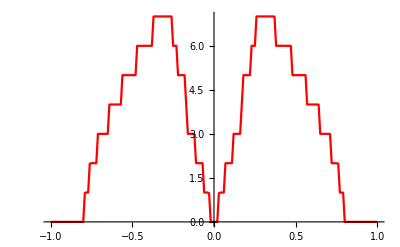

```mathematica
ListPlot[%157,Joined->True,PlotStyle->Red]
```

```mathematica
data:=data=Import["/home/shardulmukim/PhD/fwi/DFT/15AGNR/Impureza.dat"]
```

```mathematica
data[[328]]
```

{-0.339394,2.88752×10^-19,2.88752×10^-19,6.57356×10^-19,2.27654,0}

```mathematica
data[[340]][[1]]-data[[328]][[1]]
```

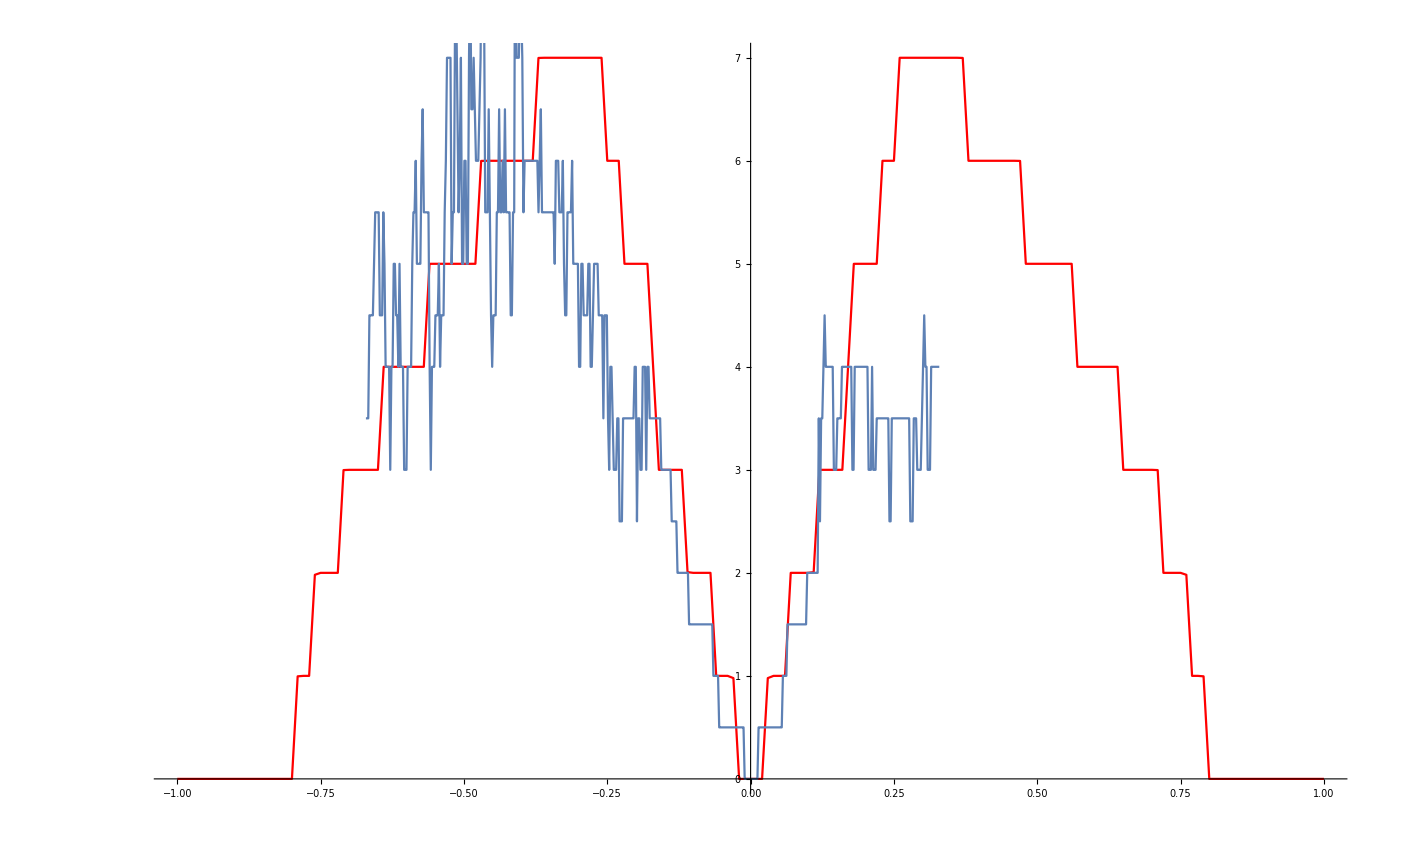

```mathematica
Show[%158,%161]
```

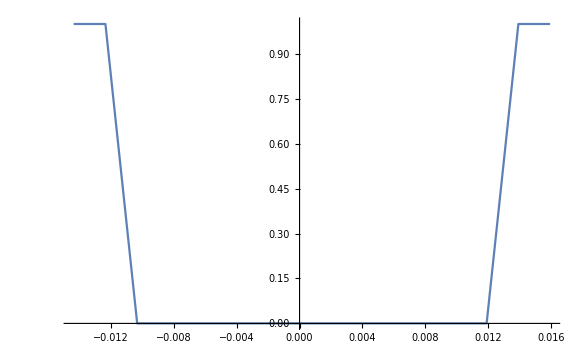

```mathematica
ListLinePlot[Table[{data[[x]][[1]]+0.329068014512349,data[[x]][[6]]},{x,326,341}]]
```

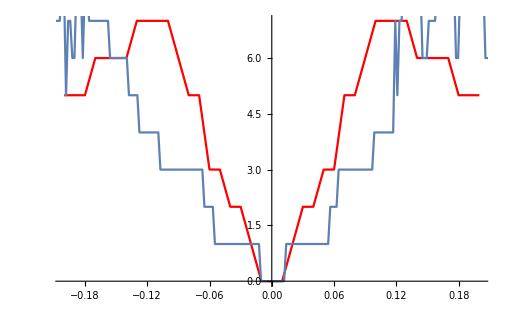

```mathematica
Show[%122,%124]
```

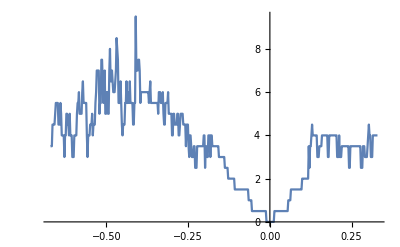

```mathematica
%161
```